## Задача 1

Уравнение Шредингера для осциллятора имеет вид
-ψ''[x]/2+x^2/2 ψ[x]=E ψ[x]
Найти 3 минимальных уровня энергии E_n  (n=0,1,2)
и нарисовать соответствующие им волновые функции
ψ_n[x].

## Решение

Уровни энергии положительны, k>0.

```mathematica
x1=1;
```

NDSolve::nlnum: The function value {1.,-0.0000838121 k} is not a list of numbers with dimensions {2} at {x,y[x],y'[x]} = {0.0000838121,0.0000838121,1.}.

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

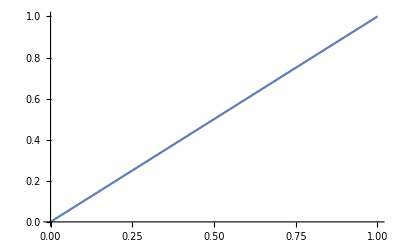

```mathematica
EE=1.49;
solution=NDSolve[{y''[x]== -k*y[x],y[0]==0,y'[0]==1},
y,{x,0,x1}][[1]];
Plot[y[x]/.solution,{x,0,x1}]
```

```mathematica
x1=1;
```

```mathematica
Manipulate[
solution=NDSolve[{y''[x]== -k*y[x],y[0]==0,y'[0]==1},
y,{x,0,x1}][[1]];
Plot[y[x]/.solution,{x,0,x1}],
{k,0,100}
]
```

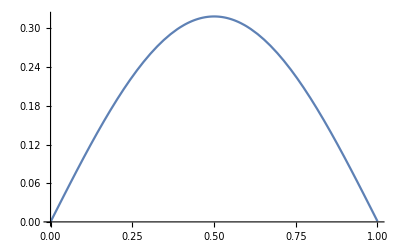

```mathematica
k=9.85;
solution=NDSolve[{y''[x]== -k*y[x],y[0]==0,y'[0]==1},
y,{x,0,x1}][[1]];
Plot[y[x]/.solution,{x,0,x1}]
```

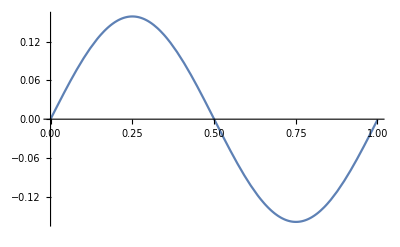

```mathematica
k=33;
Plot[y[x]/.solution,{x,0,x1}]
```

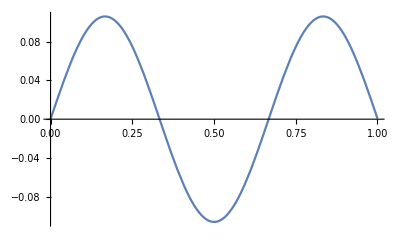

```mathematica
k=90;
Plot[y[x]/.solution,{x,0,x1}]
```